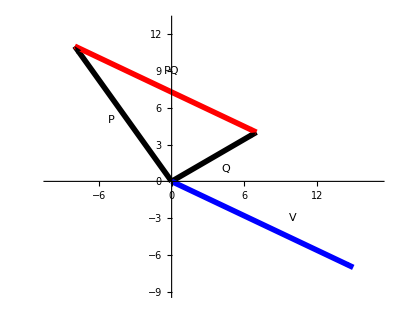

```mathematica
(* p.282《Principles of Linear Algebra with Mathematica》*)
P={-8,11};Q={7,4};
V=Q-P
ArrowPlots6=Graphics[{Arrowheads[.07],Thickness[.010],Black,Arrow[{{0,0},P}],Black,Arrow[{{0,0},Q}],Red,Arrow[{P,Q}],Blue,Arrow[{{0,0},V}]}];
TxtPlots6=Graphics[{Black,Text["P",{-5,5}],Text["Q",{4.5,1}],Text["PQ",{0,9}],Text["V",{10,-3}]}];
Show[ArrowPlots6,TxtPlots6,PlotRange-> {{-10,17},{-9,13}},Axes-> True,AxesOrigin-> {0,0}]
```

(3 | 1
2 | 4)

(3
1)

(10
10)

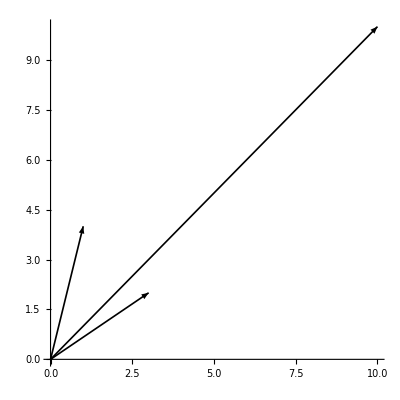

```mathematica
P={3,2};Q={1,4};K={10,10};
A = {{3,1},{2,4}};A//MatrixForm
r = {{3},{1}};r//MatrixForm
A.r//MatrixForm
ArrowPlots6=Graphics[{
Arrowheads[.03],Thickness[.003],
Black,Arrow[{{0,0},P}],
Black,Arrow[{{0,0},Q}],
Black,Arrow[{{0,0},K}]
}];
Show[ArrowPlots6,PlotRange-> {{0,10},{0,10}},Axes-> True,AxesOrigin-> {0,0}]
```